# Year 10 Curriculum

# Mathematica Bound-Reference

## Authored by gptreliance

Topic01

Linear Relations and Equations

## Performing Basic Operations

Use + for addition

Use - for subtraction

Use * for multiplication

Use / for division

Press Ctrl + / for a fraction (x/y)

Use ^ for powers, or Ctrl + 6

Use /. to substitute

Usage: equation /. variable => number

```mathematica
2a+5/.a->3
```

11

## Simplifying Expressions

Typing an expression and executing it (Shift + Enter) will automatically simplify things:

```mathematica
4a+3b-12b+4a*b
```

4 a-9 b+4 a b

Simplify[] or FullSimplify[] can also be used

```mathematica
Simplify[2x+4-3(x+1)]
```

1-x

## Factorising and Expanding

Expand expands the following

```mathematica
Expand[(x+1) (2x+1) (3x+1)]
```

1+6 x+11 x^2+6 x^3

Factor factorises the following:

```mathematica
Factor[1+6x+11 x^2+6 x^3]
```

(1+x) (1+2 x) (1+3 x)

Fancy shortcuts used: Ctrl+6 (Hat/Exponent key) for exponent (x^2)

## Solving Equations

Always use a double equals sign (‘==’, like python) or you permanently DEFINE the variable x

Usage: Solve[expression == expression2, unknown]

```mathematica
Solve[7x-1==2x+4,x]
```

{{x→1}}

## Solving Inequations

You must use Reduce[] to solve inequalities, Solve[] will not work

Usage: Reduce[expression (>, <, >= or <=) expression2, unknown]

```mathematica
Reduce[5x-1>x+4,x]
```

x>5/4

Using >= or <= (python style!) automatically simplifies to the proper symbol.

```mathematica
Reduce[20x-80>=50x-130,x]
```

x≤5/3

## Working with Fractions

This combines fractions together by putting fractional expressions over a common denominator

Usage: Together[equation of the fraction]

```mathematica
Together[(2x-1)/(x+4)^2-1/(x+4)]
```

(-5+x)/(4+x)^2

Fancy shortcuts used: Ctrl+/ (Key for division) for fraction (x/y), Ctrl+6 (Hat/Exponent key) for exponent (x^6)

## Troubleshooting Section (check at end of every lesson)

Remember to use a double equals (==) sign

Try to use Clear or ClearAll to remove accidental variable assigns

```mathematica
Clear[x]
```

Usage: Clear[some_variable_you_want_cleared], clears definitions

```mathematica
ClearAll[x,y,z]
```

Usage: ClearAll[some_variables_you_want_cleared], clears all associations, messages, values and associations

Remember, Solve command needs to know which variable needs to be found

e.g. Solve[50x-10==30x-20, x] <- That “x” needs to be stated

Variables are blue, commands are black and need to be in title case (e.g. Solve[])

Topic 01a

Linear Graphs and Functions

## Solving Simultaneous Equations

If there are multiple things going into a single parameter, use curly braces to fit them.

e.g. When solving two or more equations, the equations must be in curly braces, separated by a comma.

Remember to use double equals “==” similar to other programming languages.

```mathematica
Solve[{y==2x-1,y==3-x},{x,y}]
```

{{x→4/3,y→5/3}}

Usage: Solve[{equation_a, equation_b}, {variable_to_be_found_a, variable_to_be_found_b}]

If a variable has already been defined, don’t forget to use ClearAll.

```mathematica
ClearAll[x,y]
```

## Plotting Graphs

Plot has many parameters that can be set, depending on different use cases.

### Simple Plot

This first one is simple, equation* first, domain (x) second.

The equation does not need a y, it is only an expression.

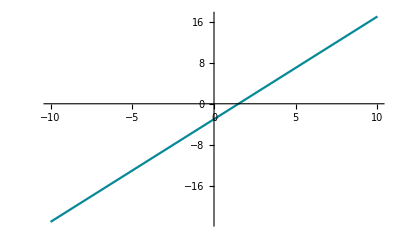

```mathematica
Plot[2x-3,{x,-10,10}]
```

Usage: Plot[equation, {domain_parameter}]

### Plotting with range (y) parameter

This second one adds a plotting range (y) to the equation. It is preceded by PlotRange ->

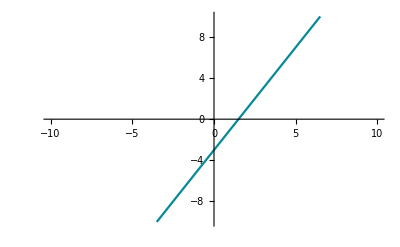

```mathematica
Plot[2x-3,{x,-10,10},PlotRange->{-10,10}]
```

Usage: Plot[equation, {domain_parameter}, PlotRange->{range_parameter}]

#### PlotRange Shortcut

You can replace “PlotRange -> {-10, 10}” with “PlotRange -> 10”, it automatically sets the range to 10 both ways of the y-axis.

```mathematica
Plot[2x-3,{x,-10,10},PlotRange->{-10,10}]
```

-Graphics-

Usage: Plot[equation, {domain_parameter}, PlotRange->{range_parameter}]

### Plotting with Multiple Equations

This one throws a second equation into the mix.

Because it involves multiple elements in a single parameter, the equations (expressions rather) are placed in curly braces {}

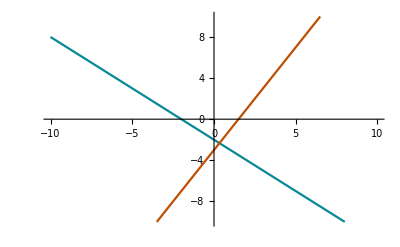

```mathematica
Plot[{-x-2,2x-3},{x,-10,10},PlotRange->{-10,10}]
```

Usage: Plot[{equation_a, equation_b}, {domain_parameter}, PlotRange->{range_parameter}]

### Adding Legends

You can add legends to the graph to know which graph belongs to which equation. This uses the PlotLegends parameter. The “Expressions” tells Mathematica to write the expression beside the legend.

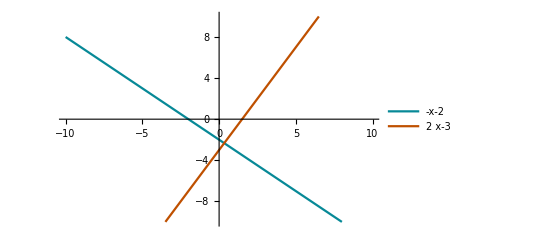

```mathematica
Plot[{-x-2,2x-3},{x,-10,10},PlotRange->{-10,10},PlotLegends->"Expressions"]
```

Usage: Plot[{equation_a, equation_b}, {domain_parameter}, PlotRange->{range_parameter}]

Topic 02

Trigonometry

## Finding sin, cos and tan

Finding these is just a trivial matter of typing the function (sin, cos, tan) and putting the degrees in the square brackets.

```mathematica
Sin[30Degree]
```

1/2

Usage: Sin[x Degree]

```mathematica
Cos[45°]
```

1/(√2)

Usage: Cos[x Degree]

Fancy shortcuts used: esc+“deg”+esc for degree symbol (°)

```mathematica
Tan[45Degree]
```

1

Usage: Tan[x Degree]

## Using ArcTan, ArcCos and ArcTan

For context, if tan(x)=1, then the angle x can be found using ArcTan.

In short, Arc(function) yields the inverse of the function.

### ArcSin[]

ArcSin yields inverse sine

```mathematica
ArcSin[1]
```

π/2

### ArcCos[]

ArcCos yields inverse cosine

```mathematica
ArcCos[0.2]
```

1.36944

### ArcTan[]

ArcTan yields inverse tangent

```mathematica
ArcTan[1]
```

π/4

### Converting Radians to Degrees

/Degree (single slash) divides by the constant Degree (equating to π/180), converting the results from radians to degrees.

```mathematica
N[ArcTan[1]/Degree]
```

45.

Fancy shortcuts used: esc+“pi”+esc for pi symbol (π)

```mathematica
N[ArcCos[2/3]/Degree]
```

48.1897

## Practical Examples/Demonstrations

### Using Sine Rule to find a side

Remember to use //N or N[] to achieve a numerical value.

```mathematica
Solve[8/Sin[42°]==a/Sin[63°],a]//N
```

{{a→10.6527}}

Fancy shortcuts used: esc+“deg”+esc for degree symbol (°)

### Using Sine Rule to find an angle

Remember to divide by Degree (/Degree, single slash)

#### Multistep Method

```mathematica
Solve[Sin[63°]/11==Sin[a]/8,Sin[a]]//N
```

{{Sin[a]→0.648005}}

Fancy shortcuts used: esc+“deg”+esc for degree symbol (°)

Copy+Paste the above radian value into ArcSin below.

```mathematica
N[ArcSin[0.6480047448642676]]/Degree
```

40.3913

#### One Liner

```mathematica
N[ArcSin[8Sin[63°]/11]]/Degree
```

40.3913

#### “More than One solutions” error workaround

```mathematica
Solve[Sin[20Degree]/8==Sin[x Degree]/15,x]//N
```

{{x→ConditionalExpression[57.2958 (2.44542+6.28319 C[1]), C[1]∈ℤ]},{x→ConditionalExpression[57.2958 (0.696175+6.28319 C[1]), C[1]∈ℤ]}}

This means there is more than one solution. 👆

The workaround is to set restrictions by using a range. There are two ways of doing this.

##### Using &&

```mathematica
Solve[Sin[20Degree]/8==Sin[x Degree]/15&&0<=x<=180,x]//N
```

{{x→39.8879},{x→140.112}}

##### Using Curly Braces

```mathematica
Solve[{Sin[20Degree]/8==Sin[x Degree]/15,0<=x<=180},x]//N
```

{{x→39.8879},{x→140.112}}

Both will yield the same result. It is up to you to choose which one to use.

### Using Cosine Rule to find a side

This command below is enough to yield exact values.

```mathematica
Solve[a^2==4^2+10^2-2*4*10Cos[45°],a]
```

{{a→-2 √(29-10 √2)},{a→2 √(29-10 √2)}}

Use //N to yield approximate values

```mathematica
Solve[a^2==4^2+10^2-2*4*10Cos[45°],a]//N
```

{{a→-7.70918},{a→7.70918}}

To discard the negatives immediately, you can use:

#### Solve

```mathematica
Solve[a==√(4^2+10^2-2*4*10Cos[45°]),a]//N
```

{{a→7.70918}}

#### Directly typing in

```mathematica
√(4^2+10^2-2*4*10Cos[45°])//N
```

7.70918

Fancy shortcuts used: esc+“deg”+esc for degree symbol (°)

### Using Cosine Rule to find an angle

#### Multistep Method

Cos Rule finding the angle opposite side 13, other two sides 8 and 11.

```mathematica
Solve[13^2==11^2+8^2-2*11*8Cos[a],Cos[a]]
```

{{Cos[a]→1/11}}

Copy+Paste the above radian value into ArcSin below.

```mathematica
N[ArcCos[1/11]]/Degree
```

84.7841

#### One Liner

```mathematica
N[ArcCos[(11^2+8^2-13^2)/(2*8*11)]]/Degree
```

84.7841

Topic03

Quadratics A&B

## Simplify

Using Simplify[] can simplify expressions

```mathematica
Simplify[(a^2+b^2)/4-(a+b)^2/4]
```

Usage: Simplify[expression]

You can also use a function from the rear. You need 2 slashes then a function.

This example is demonstrated with Simplify:

```mathematica
(a^2+b^2)/4-(a+b)^2/4//Simplify
```

-(a b)/2

Usage: expression//Simplify

Fancy shortcuts used: Ctrl+/ (Key for division) for fraction ((a^2+b^2)/4), Ctrl+6 (Hat/Exponent key) for exponent (a^2)

## Expanding

Expand expands the following:

```mathematica
Expand[(1+x)^2]
```

1+2 x+x^2

Fancy shortcuts used: Ctrl+6 (Hat/Exponent key) for exponent (x^2)

## TraditionalForm

Gives the solution a ritualistic, ordered textbook-style sequence and italics.

TraditionalForm is usually called from the rear because it is easily added on top of everything else. However it can also be called from the front.

```mathematica
Expand[(1+x)^2]//TraditionalForm
```

x^2+2 x+1

Usage: **everything else**//TraditionalForm

## Solving x-intercepts

This is just a generic Solve[] command.

Remember to use a double equals == sign and to list the x parameter.

```mathematica
Solve[(2x+3)/4==-7,x]
```

{{x→-31/2}}

Remember to use a space “ ” to separate between two variables

```mathematica
Solve[a x+c==b x-d,x]
```

{{x→(-c-d)/(a-b)}}

```mathematica
Solve[a*x+c==b*x-d,x]
```

{{x→(-c-d)/(a-b)}}

Usage: Solve[expression == y, x]

Fancy shortcuts used: Ctrl+/ (Key for division) for fraction ((2x+3)/4)

## Solving y-intercepts

#### Using Direct Substitution

Simply substituting the unknown for a number.

```mathematica
4(0)+7
```

7

Usage: expression

#### Substitution Symbol (/.)

Using the /. method to replace x.

```mathematica
4x+7/.x->0
```

7

Usage: expression /. variable -> number

#### Define Function

This one employs the idea “f of x” into the working out.

The f[x_] tells Mathematica  that x is a variable that needs replacing

```mathematica
f[x_]:=4x+7
```

Using Shift+Enter saves this function and the value can be substituted by replacing x_ with a number shown below.

```mathematica
f[0]
```

7

Usage: F[variable_]:=expression, F[substitute]

## Solving inequalities

Use Reduce[] to solve inequalities

With an inequalities and equal symbol, type the inequality first then type the equals.

The symbol will automatically merge if you are correct.

```mathematica
Reduce[(-2x+3)/4>=1,x]
```

x≤-1/2

Usage: Reduce[expression,variable_to_be_found]

Fancy shortcuts used: Ctrl+/ (Key for division) for fraction ((-2x+3)/4)

## Discriminant

With known coefficients

```mathematica
Discriminant[10 x^2+3mx+7,x]
```

-40 (7+3 mx)

author’s note: this behaviour is indeed, strange.

```mathematica
9 m^2-(4*10*7)
```

-280+9 m^2

Usage: Discriminant[expression, variable]

With unknown coefficient

```mathematica
Discriminant[4 x^2+10x+7,x]
```

-12

Usage: Discriminant.14.14[expression, variable]

## Finding Quadratic Rules with three unknowns

Find the rule of the quadratic if it goes through the coordinates (1,-4),(-1,10) and (3,-2)

```mathematica
f[x_]:=a x^2+b x+c
```

Remember to use a space to separate the variables so they can multiply.

```mathematica
Solve[{f[1]==-4,f[-1]==10,f[3]==-2},{a,b,c}]
```

{{a→2,b→-7,c→1}}

Therefore:

y=2 x^2-7x+1

## Finding Quadratic Rules in intercept form

Find the equation of the quadratic which goes through the x-intercepts 2 and -3 and also goes through the point (4,5)

```mathematica
(*y=a(x-x1)(x-x2)
sub in x-intercepts then sub in known other point and solve for a*)
Solve[4==a(x-2)(x+3),a]/.x->5
```

{{a→1/6}}

Therefore

y=1/6(x-2)(x+3)

## Plot two graphs on a single axes

Remember to use curly braces {} as there is more than one expression.

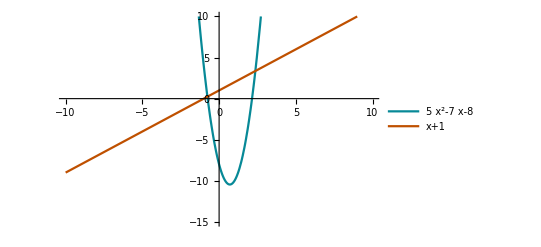

```mathematica
Plot[{5 x^2-7x-8,x+1},{x,-10,10},PlotRange->{-15,10},PlotLegends->"Expressions"]
```

## Finding Points of Intersection

### Set both equations equal to one another which use x and y

Find the point of intersection between y=5 x^2-7x-8 and y=x+1

```mathematica
Solve[{y==5 x^2-7x-8,y==x+1},{x,y}]//TraditionalForm
```

{{x→1/5 (4-√61),y→1/5 (9-√61)},{x→1/5 (4+√61),y→1/5 (9+√61)}}

Therefore, POIs are:

(((4-√61)/5,(9-√61)/5),((4+√61)/5,(9+√61)/5))

Fancy shortcuts used: Ctrl+/ (Key for division) for fraction ((4-√61)/5), Ctrl+2 for square root (√61)

### Set both equations equal to one another and solve for x, then sub into either equation for y

Find the point of intersection between y=5 x^2-7x-8 and y=x+1

```mathematica
Solve[5 x^2-7x-8==x+1,x]
```

{{x→1/5 (4-√61)},{x→1/5 (4+√61)}}

```mathematica
x+1/.x->{{1/5 (4-√61)},{1/5 (4+√61)}}
```

{{1+1/5 (4-√61)},{1+1/5 (4+√61)}}

Therefore, POIs are:

(((4-√61)/5,(9-√61)/5),((4+√61)/5,(9+√61)/5))

## Finding the Turning Point

### FindMinimum and FindMaximum

```mathematica
FindMinimum[4 x^2+10x+7,x]
```

{0.75,{x→-1.25}}

Rationalize can be used from the front, or from the rear, to output the answer as exact values.

```mathematica
Rationalize[FindMinimum[4 x^2+10x+7,x]](*Front*)
```

{3/4,{x→-5/4}}

```mathematica
FindMinimum[4 x^2+10x+7,x]//Rationalize(*Rear*)
```

{3/4,{x→-5/4}}

FindMaximum[] example:

```mathematica
FindMaximum[-x^2+4x+3,x]//Rationalize
```

{7,{x→2}}

### Use -b/(2a) and Substituting

For example, Let y=5 x^2-7x-8

```mathematica
(-(-7))/(2(5))
```

7/10

Remember to use parenthesis for double negatives

This is bad: --7

This is good: -(-7)

```mathematica
5 x^2-7x-8/.x->7/10
```

-209/20

Therefore, TP = (7/10,209/20)

### Halfway between the two x intercepts then sub into the original equation

```mathematica
Solve[5 x^2-7x-8==0,x]
```

{{x→1/10 (7-√209)},{x→1/10 (7+√209)}}

```mathematica
(1/10(7-√209)+1/10(7+√209))/2//Simplify
```

7/10

Therefore TP = (7/10,209/20)

### Complete the square

This is an example of a single-line algorithm

```mathematica
compsq[a_,b_,c_]:=a(x+b/(2a))^2+c-b^2/(4a)//TraditionalForm
compsq[1,2,4]
```

(x+1)^2+3

Topic 04

Probability

## Measures of Centre

### Mean

Remember your curly braces {}.

```mathematica
Mean[{1,2,3,6}]
```

3

### Median

Remember your curly braces {}.

```mathematica
Median[{1,2,3,6}]
```

5/2

## 5-Figure Summary

```mathematica
Min[{1,2,3,4,5,6}]
```

1

```mathematica
Quantile[{1,2,3,4,5,6},1/4]
```

2

```mathematica
Median[{1,2,3,6}]
```

5/2

```mathematica
Quantile[{1,2,3,4,5,6},3/4]
```

5

```mathematica
Max[{1,2,3,4,5,6}]
```

6

## Measures of Spread

```mathematica
InterquartileRange[{1,2,3,4,5,6}]
```

3

```mathematica
MeanDeviation[{1,2,3,4,5,6}]
```

3/2

```mathematica
StandardDeviation[{1,2,3,4,5,6}]
```

√(7/2)

## Box and Whisker Chart

Creates a box and whisker chart. Hovering the cursor over it also shows the 5-figure summary.

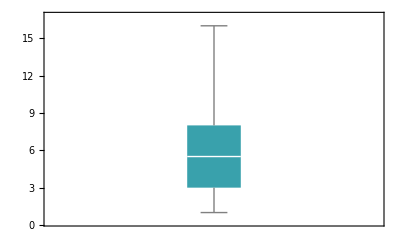

```mathematica
BoxWhiskerChart[{1,2,3,4,5,6,7,8,9,16}]
```

## Box Plots

### Parallel Box Plots

#### Data

```mathematica
Data1={1020,1150,980,1210,1090,990,1120,1050,1180,1070,1130,1040,1190,1110,1000,1230,1080,1170,995,1140}
```

{1020,1150,980,1210,1090,990,1120,1050,1180,1070,1130,1040,1190,1110,1000,1230,1080,1170,995,1140}

```mathematica
Data2={780,850,720,890,810,740,880,800,910,830,860,770,900,820,750,930,790,870,730,840}
```

{780,850,720,890,810,740,880,800,910,830,860,770,900,820,750,930,790,870,730,840}

#### Box Plot

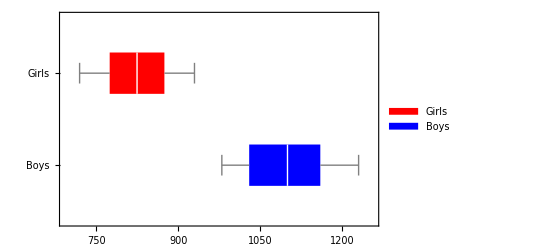

```mathematica
BoxWhiskerChart[{Data1,Data2},"Outliers",ChartLabels->{"Boys","Girls"},ChartLegends->{"Boys","Girls"},ChartStyle->{Blue,Red},BarOrigin->Left]
```

### Showing Outliers on the Graph

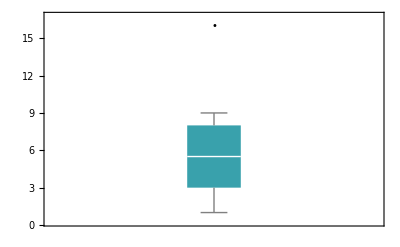

```mathematica
BoxWhiskerChart[{1,2,3,4,5,6,7,8,9,16},"Outliers"]
```

## Creating Histograms

Histogram[data] automatically creates a histogram of the data. It can work from a stored value (variable) or executed from a single line.

```mathematica
data = {68.38,50.02,33.82,51.46,50.02,68.42,70.72,69.1,76.12,48.4,71.08,69.28,48.58,50.56,68.02,55.78,52.18,59.2,53.8,64.96,70.9,49.12,61.36,51.64,53.08,46.24,60.28,45.7,47.5,70.18,64.78,66.4,41.74,57.94,73.24,80.26,61.9,45.16,60.64,48.58}
```

{68.38,50.02,33.82,51.46,50.02,68.42,70.72,69.1,76.12,48.4,71.08,69.28,48.58,50.56,68.02,55.78,52.18,59.2,53.8,64.96,70.9,49.12,61.36,51.64,53.08,46.24,60.28,45.7,47.5,70.18,64.78,66.4,41.74,57.94,73.24,80.26,61.9,45.16,60.64,48.58}

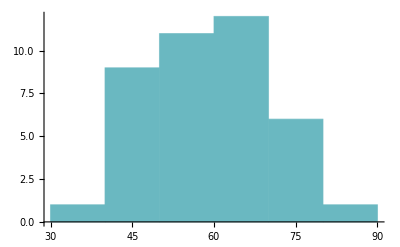

```mathematica
Histogram[data]
```

Single-line execution

```mathematica
Histogram[{68.38,50.02,33.82,51.46,50.02,68.42,70.72,69.1,76.12,48.4,71.08,69.28,48.58,50.56,68.02,55.78,52.18,59.2,53.8,64.96,70.9,49.12,61.36,51.64,53.08,46.24,60.28,45.7,47.5,70.18,64.78,66.4,41.74,57.94,73.24,80.26,61.9,45.16,60.64,48.58}]
```

-Graphics-

More options can be added as well.

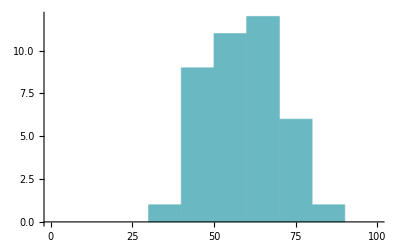

```mathematica
Histogram[data,{0,100,10}]
```

Usage: Histogram[data,{xmin,xmax,dx}]

## Importing Data

Import data from an existing file *.xlsx

```mathematica
Testdata = Import["C:\Users\(user)\Desktop\sleep_data.xlsx"]
```

Import::nffil: File C:\Users\(user)\Desktop\sleep_data.xlsx not found during Import.

$Failed

Topic 05

Exponentials and Logarithms

## Using Exponentials and Logs

### Logging with Euler’s Number ϵ

```mathematica
Log[ⅇ]
```

1

Fancy Shortcuts Used: Esc:ee:Esc for Euler’s Number ϵ

Alternatively, a capital e (E) can be used.

```mathematica
Log[E]
```

1

### Logging with Custom Bases

Using Log10 sets the base to 10.

```mathematica
Log10[10]
```

1

10 can be changed to any number for a different base.

```mathematica
Log2[2]
```

1

Alternatively, using Log[base,x] works just as well.

```mathematica
Log[5,x]
```

Log[x]/Log[5]

Fancy Shortcuts Used: Ctrl+/ for Fraction (Log[x]/Log[5])

## Plotting Exponentials with Horizontal Asymptotes

Use the Plot[] command with curly braces {} wherever multiple arguments are processed. The PlotRange command determines how much vertical space is shown.

### Using PlotStyle

PlotStyle denotes how the lines will be styled in respective order. Additional elements such as dashes can be included in a pair of curly braces {}.

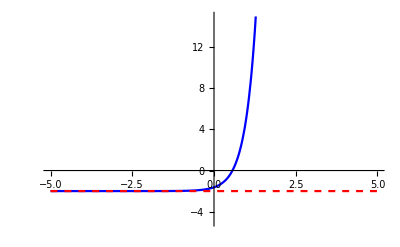

```mathematica
Plot[{ⅇ^(3x-1)-2,-2},{x,-5,5},PlotRange->{-5,15},PlotStyle->{Blue,{Red,Dashed}}]
```

Fancy Shortcuts Used: Esc:ee:Esc for Euler's Number ϵ

### Using GridLines

Usage: GridLines->{line_on_x_axis, line_on_y_axis}

GridLinesStyle->Directive[colour, style]

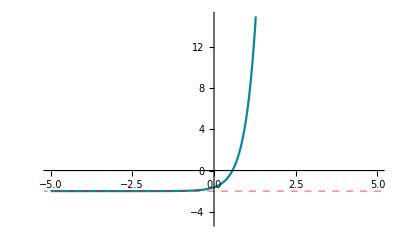

```mathematica
Plot[ⅇ^(3x-1)-2,{x,-5,5},PlotRange->{-5,15},GridLines->{None,{-2}},GridLinesStyle->Directive[Red,Dashed]]
```

Fancy Shortcuts Used: Esc:ee:Esc for Euler' s Number ϵ

## Plotting Logarithms with Vertical Asymptotes

Similar to GridLines from above, enter a value for the x-axis, but not y, because this is a vertical asymptote.

Don't include "y =" !

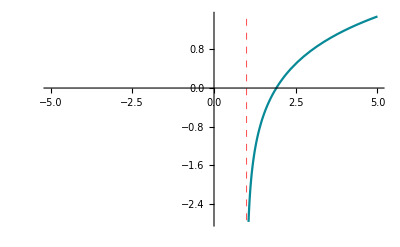

```mathematica
Plot[Log[3(x-1)]-1,{x,-5,5},GridLines->{{1},None},GridLinesStyle->Directive[Red,Dashed]]
```

## Solving Equations including Exponentials and Logarithms

It just solves.

Remember to include Reals to yield a real number.

### Without Reals

```mathematica
Solve[ⅇ^(3x-2)==4,x]
```

{{x→ConditionalExpression[1/3 (2+2 ⅈ π C[1]+Log[4]), C[1]∈ℤ]}}

### With Reals

```mathematica
Solve[ⅇ^(3x-2)==4,x,Reals]
```

{{x→2/3 (1+Log[2])}}